# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\Chaotic_eigenfunctions\Coupled kicked top

```mathematica
(*Operators*)
Clear[Sz,SM,Sm,Sx,Sy];
Sz[J_]:=DiagonalMatrix[Table[-J+k-1,{k,1,2J+1}]];
SM[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i+1)],{i,-J,J-1}],1];
Sm[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i-1)],{i,-J+1,J}],-1];
Sx[J_]:=(1/2)(SM[J]+Sm[J]);
Sy[J_]:=Sy[J]=(1/(2I))(SM[J]-Sm[J]);
Clear[Floq];
Floq[J_,α_,k_,τ_]:=N[MatrixExp[(-I*k/(2J))(Sx[J].Sx[J])].MatrixExp[(-I*α*τ)(Sz[J])]];
Clear[a2];
a2[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J,J}],20]]
];
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\Mathematica_packages\\QMB.wl"]
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\Mathematica_packages\\Chaometer.wl"]
```

# Method

```mathematica
Clear[haar];
haar[dim_Integer]:=Module[{l=2*dim+1,state1},
state1=Table[RandomReal[NormalDistribution[],2],{l}];
Normalize[state1[[All,1]]+I state1[[All,2]]]
];
```

```mathematica
radius=1.99999;
delta=0.020;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
boundaryPoints=(radius)Table[{Cos[i],Sin[i]},{i,0,2Pi,Pi/100}];
circlePoints=Select[gridPoints,Norm[#]<radius&];
region=Join[boundaryPoints,circlePoints];
region//Length
```

31602

```mathematica
ListPlot[region,AspectRatio->1];
```

```mathematica
Clear[J];
J=100;
α=0.84;
τ=1;
```

```mathematica
rotation=MatrixExp[I(N[Pi])Sx[J]];
rotation2=MatrixExp[I(N[α/2])Sz[J]];
rotation3=MatrixExp[I(N[-α/2])Sz[J]];
```

```mathematica
cohes=ParallelTable[Quiet[a2[J,i[[1]],i[[2]]]],{i,region}];
```

```mathematica
Clear[husimi];
husimi[ψ_]:=ParallelTable[{region[[i,1]],region[[i,2]],Abs[Conjugate[cohes[[i]]].ψ]^2},{i,Length[region]}]
```

```mathematica
k=100α;
mat=ConjugateTranspose[rotation2].Floq[J,α,k,τ].rotation2;
(*mat=ConjugateTranspose[rotation3].ConjugateTranspose[rotation].Floq[J,α,k,τ].rotation.rotation3;*)
matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
eigenvalM=Eigenvalues[matM];
eigenvalm=Eigenvalues[matm];
matm=Table[mat[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
eigenvecM=Eigenvectors[matM];
eigenvecm=Eigenvectors[matm];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
```

```mathematica
data=husimi[neweigenvec[[2]]];
```

```mathematica
ListDensityPlot[data,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",ImageSize->500,PlotLabel->Style["Husimi function of Eigenvector",25,Black]]
```

-Graphics-

```mathematica
d2=ParallelTable[Total[Abs[Conjugate[neweigenvec].i]^4],{i,cohes}];
```

```mathematica
newd2=Transpose[{region[[All,1]],region[[All,2]],-Log[d2]/Log[2J+1]}];
```

```mathematica
d2plotn=ListDensityPlot[newd2,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["North D_2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k],25,Black],ImageSize->800]
```

```mathematica
d2plots=ListDensityPlot[newd2,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["South D_2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta],25,Black],ImageSize->800]
```

```mathematica
Export["d2north_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>".png",d2plotn]
```

d2north_J_100_alpha_0.84_k_2.5.png

```mathematica
Export["d2south_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[delta]<>".png",d2plots]
```

d2south_J_100_alpha_0.84_k_2.5_dq_0.03.png

```mathematica
allhusimis=Table[husimi[i],{i,neweigenvec}];
newhusimis=Table[Transpose[{i[[All,1]],i[[All,2]],i[[All,3]]/Total[i[[All,3]]]}],{i,allhusimis}];
iprs=Table[Total[Abs[i[[All,3]]]^2],{i,newhusimis}];
```

```mathematica
sorted=Sort[iprs];
index=Table[Flatten[Position[iprs,sorted[[i]]]],{i,2J+1}];
sortedeigenvec=Table[neweigenvec[[i[[1]]]],{i,index}];
```

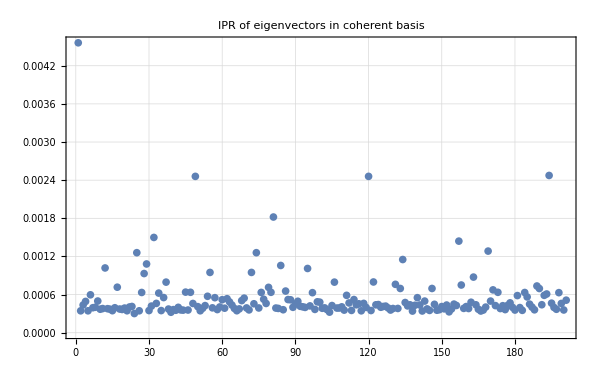

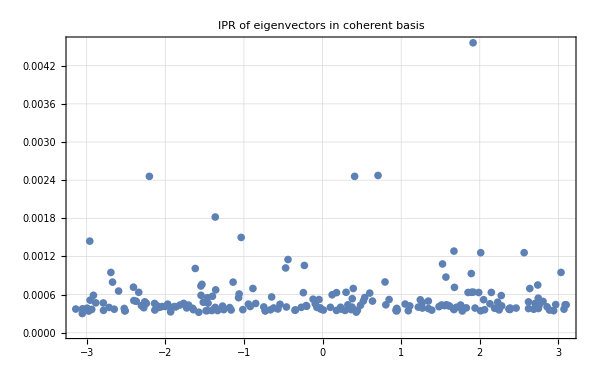

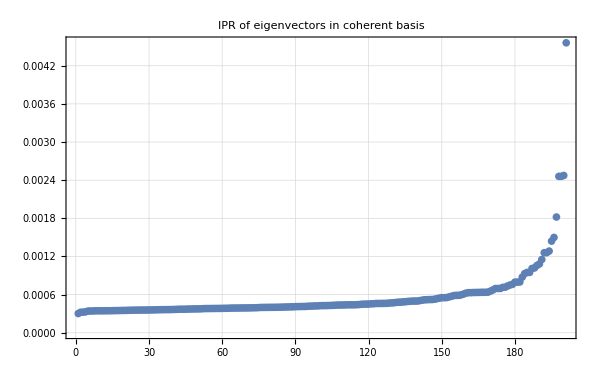

```mathematica
ListPlot[iprs,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["IPR of eigenvectors in coherent basis",25,Black],ImageSize->600]
ListPlot[Transpose[{Arg[neweigenval],iprs}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["IPR of eigenvectors in coherent basis",25,Black],ImageSize->600]
ListPlot[Sort[iprs],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["IPR of eigenvectors in coherent basis",25,Black],ImageSize->600]
```

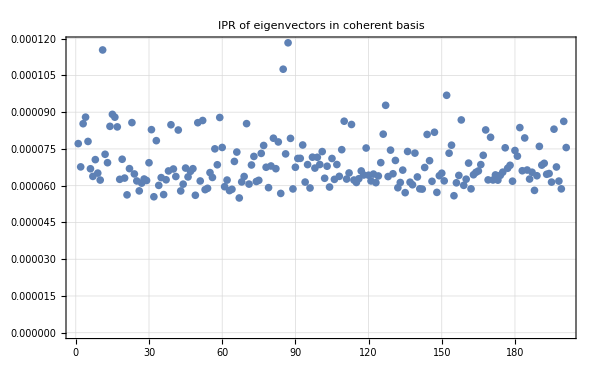

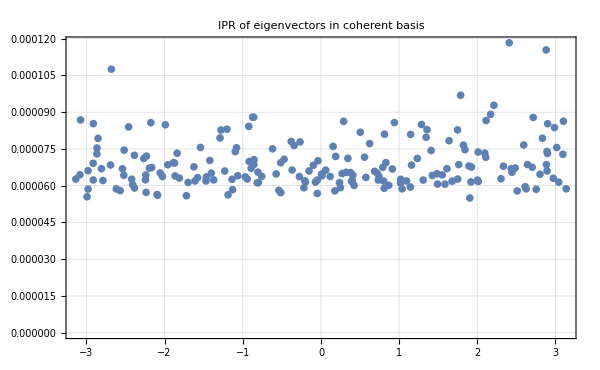

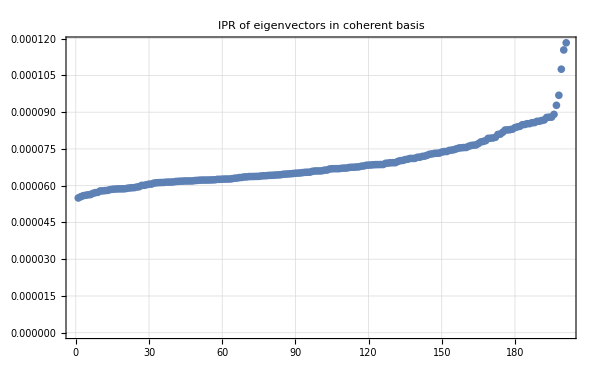

```mathematica
ListPlot[iprs,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["IPR of eigenvectors in coherent basis",25,Black],ImageSize->600]
ListPlot[Transpose[{Arg[neweigenval],iprs}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["IPR of eigenvectors in coherent basis",25,Black],ImageSize->600]
ListPlot[Sort[iprs],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["IPR of eigenvectors in coherent basis",25,Black],ImageSize->600]
```

```mathematica
iprsdicke=ParallelTable[Total[Abs[i]^4],{i,sortedeigenvec}];
```

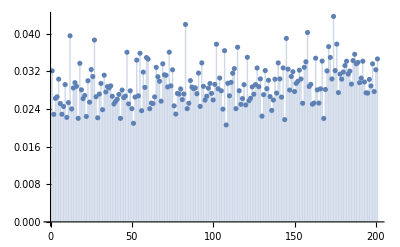

```mathematica
ListPlot[iprsdicke,PlotRange->All,Filling->Axis]
```

```mathematica
husi1=husimi[sortedeigenvec[[-1]]];
husi2=husimi[sortedeigenvec[[-2]]];
husi3=husimi[sortedeigenvec[[-3]]];
```

```mathematica
ListDensityPlot[husi1,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["Most localized eigenvector",25,Black]]
ListDensityPlot[husi2,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["Most delocalized eigenvector",25,Black]]
ListDensityPlot[husi3,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["Most delocalized eigenvector",25,Black]]
```

-Graphics-

-Graphics-

-Graphics-

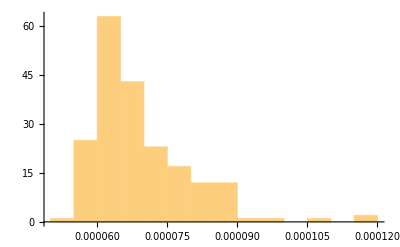

```mathematica
Histogram[iprs,15]
```

```mathematica
Do[

Export["northeigenvec_"<>ToString[i]<>"_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[delta]<>".png",ListDensityPlot[allhusimis[[i]],PlotRange->{All,All,{0,1}},PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North Eigenvec "<>ToString[i]<>", J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->1000,ColorFunction->"BlueGreenYellow"]]

,{i,2J+1}]
```

```mathematica
Clear[husimiq];
husimiq[ψ_,q_]:=ParallelTable[{region[[i,1]],region[[i,2]],Abs[Conjugate[cohes[[i]]].ψ]^q},{i,Length[region]}]
```

```mathematica
husi3a=husimiq[sortedeigenvec[[-2]],0.1];
husi3b=husimiq[sortedeigenvec[[-2]],0.25];
husi3c=husimiq[sortedeigenvec[[-2]],0.5];
husi3d=husimiq[sortedeigenvec[[-2]],0.99];
husi3e=husimiq[sortedeigenvec[[-2]],2];
husi3f=husimiq[sortedeigenvec[[-2]],4];
husi3g=husimiq[sortedeigenvec[[-2]],8];
```

```mathematica
ListDensityPlot[husi3a,PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North Eigenvec "<>ToString[1]<>", J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->800,ColorFunction->"BlueGreenYellow"]
ListDensityPlot[husi3b,PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North Eigenvec "<>ToString[1]<>", J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->800,ColorFunction->"BlueGreenYellow"]
ListDensityPlot[husi3c,PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North Eigenvec "<>ToString[1]<>", J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->800,ColorFunction->"BlueGreenYellow"]
ListDensityPlot[husi3d,PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North Eigenvec "<>ToString[1]<>", J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->800,ColorFunction->"BlueGreenYellow"]
ListDensityPlot[husi3e,PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North Eigenvec "<>ToString[1]<>", J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->800,ColorFunction->"BlueGreenYellow"]
ListDensityPlot[husi3f,PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North Eigenvec "<>ToString[1]<>", J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->800,ColorFunction->"BlueGreenYellow"]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
ListPlot[{Abs[sortedeigenvec[[1]]]^2,Abs[sortedeigenvec[[174]]]^2},PlotRange->All,Filling->Axis,PlotTheme->"Detailed"]
```

-Graphics-

```mathematica
ListPlot[Abs[sortedeigenvec[[-2]]]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed"]
```

-Graphics-

```mathematica
husi3g=husimiq[sortedeigenvec[[-3]],0.1];
```

## Random states

```mathematica
random=Table[haar[100],{i,20}];
```

```mathematica
data=Table[husimi[i],{i,random}];
```

```mathematica
Table[ListDensityPlot[i,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",ImageSize->500,PlotLabel->Style["Husimi function of Eigenvector",25,Black]],{i,data}];
```

```mathematica
average=Mean[data];
```

```mathematica
average//Dimensions
```

{14153,3}

```mathematica
Table[Histogram[i[[All,3]]],{i,data}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Histogram[average[[All,3]]]
```

-Graphics-

```mathematica
ListDensityPlot[average,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",ImageSize->500,PlotLabel->Style["Average Husimi function",25,Black]]
```

-Graphics-

```mathematica
random1=haar[100];
random2=Normalize[Sum[RandomReal[]*i,{i,neweigenvec}]];
random3=Normalize[Sum[Exp[I*RandomReal[{-Pi,Pi}]]*RandomReal[]*i,{i,neweigenvec}]];
```

```mathematica
ListDensityPlot[husimi[random1],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",ImageSize->500,PlotLabel->Style["Husimi function of Eigenvector",25,Black]]
ListDensityPlot[husimi[random2],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",ImageSize->500,PlotLabel->Style["Husimi function of Eigenvector",25,Black]]
ListDensityPlot[husimi[random3],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",ImageSize->500,PlotLabel->Style["Husimi function of Eigenvector",25,Black]]
```

-Graphics-

-Graphics-

-Graphics-

## Scaling

```mathematica
Qs=Table[{Rationalize[i],75/100},{i,0.5,1.0,0.01}];
k=100α;
Qs=(rot[-θ].#&/@Qs);
```

```mathematica
data={};
Do[

cohes=ParallelTable[Quiet[a2[J,i[[1]],i[[2]]]],{i,Qs}];
rotation2=MatrixExp[I(N[α/2])Sz[J]];
mat=ConjugateTranspose[rotation2].Floq[J,α,k,τ].rotation2;
matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
eigenvalM=Eigenvalues[matM];
eigenvalm=Eigenvalues[matm];
matm=Table[mat[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
eigenvecM=Eigenvectors[matM];
eigenvecm=Eigenvectors[matm];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
cohefloq=ParallelTable[Conjugate[neweigenvec].i,{i,cohes}];
ipr=ParallelTable[Total[Abs[i]^4],{i,cohefloq}];
AppendTo[data,{J,ipr}];

,{J,1,100}];
```

```mathematica
data//Dimensions
```

{100,2}

```mathematica
data[[1]]
```

{1,{0.333577,0.333552,0.33356,0.333603,0.333682,0.333797,0.333949,0.334137,0.334363,0.334627,0.334928,0.335268,0.335646,0.336063,0.336518,0.337011,0.337543,0.338113,0.338721,0.339367,0.34005,0.340769,0.341524,0.342315,0.343141,0.344,0.344892,0.345816,0.346772,0.347756,0.34877,0.34981,0.350876,0.351967,0.353079,0.354213,0.355366,0.356537,0.357722,0.358922,0.360132,0.361352,0.362578,0.36381,0.365044,0.366277,0.367508,0.368734,0.369953,0.371161,0.372356}}

```mathematica
jlist=Range[1,100];
```

```mathematica
newdata=Table[Transpose[{Log[2*i+1],Log[data[[i,2,j]]]}],{j,Length[Qs]},{i,100}];
```

```mathematica
ListPlot[{newdata[[1]],newdata[[25]],newdata[[-1]]},PlotRange->All,Joined->True,PlotTheme->"Detailed", ImageSize->1200]
```

-Graphics-

# Hamiltonian

```mathematica
α=0.84;
τ=1;
k=0.5;
J=20;
```

```mathematica
mat1=Floq[J,α,30.,τ];
mat2=Floq[J,α,k,τ];
mat3=KroneckerProduct[mat1,mat2];
```

```mathematica
ϵ=0.5;
mat4=MatrixExp[(-I*ϵ/Sqrt[J*J])KroneckerProduct[N[Sz[J]],N[Sz[J]]]];
```

```mathematica
mat=mat4.mat3;
```

```mathematica
matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
eigenvalM=Eigenvalues[matM];
eigenvalm=Eigenvalues[matm];
matm=Table[mat[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
eigenvecM=Eigenvectors[matM];
eigenvecm=Eigenvectors[matm];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
```

```mathematica
{eigenval,eigenvec}=Eigensystem[mat];
```

```mathematica
ComplexListPlot[eigenval,PlotTheme->"Detailed",AspectRatio->1,PlotRange->All]
```

-Graphics-

```mathematica
iprs=ParallelTable[Total[Abs[i]^4],{i,eigenvec}];
```

```mathematica
ListPlot[Transpose[{Arg[eigenval],iprs}],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[Transpose[{Arg[eigenval],iprs}],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[Transpose[{Arg[eigenval],iprs}],PlotRange->All]
```

-Graphics-

# Quantum channel

```mathematica
Ja=10;
Jb=5;
a=5;
c=5;
```

```mathematica
mata=MatrixExp[-I*a*(N[KroneckerProduct[Sz[Ja],IdentityMatrix[2Jb+1]]]+N[KroneckerProduct[IdentityMatrix[2Ja+1],Sz[Jb]]])];
matb=MatrixExp[(-I*c/Sqrt[Ja*Jb])(N[KroneckerProduct[Sx[Ja],Sx[Jb]]])];
mat=mata.matb;
```

```mathematica
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[mat]]]];
```

```mathematica
ComplexListPlot[eigenval,PlotTheme->"Detailed",AspectRatio->1,PlotRange->All]
```

-Graphics-

```mathematica
iprs=ParallelTable[Total[Abs[i]^4],{i,eigenvec}];
```

```mathematica
ListPlot[Transpose[{Arg[eigenval],iprs}],PlotTheme->"Detailed",PlotRange->All,ImageSize->600,Filling->Axis,PlotLabel->Style["a = "<>ToString[a]<>", c = "<>ToString[c]<>", Ja = "<>ToString[Ja]<>" Jb = "<>ToString[Jb],25,Black],FrameLabel->{Style["ϕ",20,Black],Rotate[Style["IPR",20,Black],-90Degree]}]
```

-Graphics-

```mathematica
Clear[reshuf];
reshuf[matrix_,dimA_,dimB_]:=Module[{dims,reshuffled},dims={dimA,dimB};
ArrayReshape[Transpose[ArrayReshape[matrix,Join[dims,dims]],{1,3,2,4}],{dimA dimB,dimA dimB}]
];
Clear[reshape];
reshape[matrix_,dimA_,dimB_]:=ArrayFlatten[ArrayReshape[matrix,{dimA,dimB,dimA,dimB}]];
```

```mathematica
ψ=a2[Jb,1,0];
```

```mathematica
mat//Dimensions
```

{231,231}

```mathematica
UR=reshape[mat,2Ja+1,2Jb+1];
UR//Dimensions
```

{441,121}

```mathematica
Dyad[ψ]//Dimensions
```

{11,11}

```mathematica
SparseArray@KroneckerProduct[IdentityMatrix[2Jb+1]/(2Jb+1),Dyad[ψ]]//Dimensions
```

{121,121}

```mathematica
choi=Chop[UR.SparseArray@KroneckerProduct[IdentityMatrix[2Jb+1]/(2Jb+1),Dyad[ψ]].ConjugateTranspose[UR]];
```

```mathematica
eigenchoi=Sort[Chop[Eigenvalues[choi]]];
```

```mathematica
ListPlot[eigenchoi,PlotRange->All]
```

-Graphics-

```mathematica
{eval,evec}=Transpose[Sort[Transpose[Eigensystem[choi]]]];
```

```mathematica
evec//Dimensions
```

{441,441}

```mathematica
newevec=Table[ArrayReshape[i,{2Ja+1,2Ja+1}],{i,evec}];
```

```mathematica
newevec[[1]]//Dimensions
```

{21,21}

```mathematica
Sum[ConjugateTranspose[i].i,{i,newevec}]//Dimensions
```

{21,21}

```mathematica
Total[ConjugateTranspose[#].#&/@newevec]//Dimensions
```

{21,21}

```mathematica
norm=Table[Total[ConjugateTranspose[#].#&/@i],{i,newevec}]//Chop
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
Clear[Ft];
Ft[n_]:=MatrixPower[mat,n];
```

```mathematica
evol=Table[Ft[i],{i,0,20}];
```

```mathematica
id=IdentityMatrix[2Jb+1]/(2Ja+1);
```

```mathematica
URt=Table[reshape[i,2Ja+1,2Jb+1],{i,evol}];
```

```mathematica
choist=Table[i.(SparseArray@KroneckerProduct[id,Dyad[ψ]]).ConjugateTranspose[i],{i,URt}];
```

```mathematica
choist//Dimensions
```

{21,441,441}

```mathematica
eigenchoit=Table[Sort[Chop[Eigenvalues[i]]],{i,choist}];
```

```mathematica
ListPlot[Transpose[eigenchoit],PlotRange->All,PlotTheme->"Detailed",ImageSize->700,Joined->True]
```

-Graphics-

```mathematica
choipurities=Table[Total[i^2],{i,eigenchoit}];
```

```mathematica
ListPlot[choipurities,PlotRange->All,PlotTheme->"Detailed",ImageSize->700,Joined->True]
```

-Graphics-

```mathematica
threshold=0.01;
```

```mathematica
nonzero=Table[Count[i,_?(#>threshold&)],{i,eigenchoit}];
```

```mathematica
ListPlot[nonzero]
```

-Graphics-